```mathematica
(*


Get the random cayley graphs with fixed degree 

*)

Basegenertors = RandomPermutation[DihedralGroup[10], 3]



(*Basegenertors = {Cycles[{{1,2}}], Cycles[{{2,3}}]}*)
BaseGroup =  PermutationGroup[Basegenertors]
BaseGroup // GroupOrder;

SnCayley = CayleyGraph[BaseGroup]
```

{Cycles[{{1,7},{2,6},{3,5},{8,10}}],Cycles[{{1,6},{2,7},{3,8},{4,9},{5,10}}],Cycles[{{1,6},{2,5},{3,4},{7,10},{8,9}}]}

PermutationGroup[{Cycles[{{1,7},{2,6},{3,5},{8,10}}],Cycles[{{1,6},{2,7},{3,8},{4,9},{5,10}}],Cycles[{{1,6},{2,5},{3,4},{7,10},{8,9}}]}]

-Graphics-

```mathematica
BaseAdj = AdjacencyMatrix[SnCayley]  // MatrixForm; 
Basedegree = Length @ Basegenertors;

Basedim =  VertexCount[SnCayley];
Basevertices  = BaseGroup// GroupElements;
```

```mathematica
BaseEgdeLeft[idx_] := Module[{ lst , g, i, j ,h, generator}, 
lst = {};
g = Basevertices[[idx]]; 	
				
For [j =1, j <= Length @ Basevertices , j++, 
		h = Basevertices[[j]];
	 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];

If[g == PermutationProduct[generator,h], AppendTo[lst, {idx, j, i}]]
] ;
];
lst
]; 


BaseEgdeRight[idx_] := Module[{ lst , g, i, j ,h, generator}, 
lst = {};
g = Basevertices[[idx]]; 	
				
For [j =1, j <= Length @ Basevertices , j++, 
		h = Basevertices[[j]];
	 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];

If[g == PermutationProduct[h, generator], AppendTo[lst, {idx, j, i}]]
] ;
];
lst
]; 

BaseEgdeLeft[6] (* src, dest, path *)
BaseEgdeRight[3]
```

{{6,15,3},{6,16,2},{6,17,1}}

{{3,10,3},{3,12,1},{3,13,2}}

```mathematica
StoreInfoLeft = Flatten[Table[BaseEgdeLeft[i], {i, 1, Basedim}], 1];
StoreInfoRight = Flatten[Table[BaseEgdeRight[i], {i, 1, Basedim}], 1];
```

```mathematica
GetIncEdgesLeft[idx_] :=  Module[{ lst , g1,g2, i, generator,  }, (* use the StoreInfoRight *)
lst = {};
g1 = Basevertices[[idx[[1]]]];
(*Print[g1]*);
g2 = Basevertices[[idx[[2]]]];
				 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];
h1dex = Flatten[Position[Basevertices, PermutationProduct[generator, g1]]][[1]]; 
(*Print[ PermutationProduct[generator, g1]]; *)
h2dex = Flatten[Position[Basevertices, PermutationProduct[generator, g2]]][[1]]; 

If[MemberQ[StoreInfoRight, {h1dex, h2dex, idx[[3]]}], AppendTo[lst, {idx, {h1dex, h2dex, idx[[3]]}}]]
] ;
lst
]; 

GetIncEdgesRight[idx_] :=  Module[{ lst , g1,g2, i, generator,  }, (* use the StoreInfoRight *)
lst = {};
g1 = Basevertices[[idx[[1]]]];
(*Print[g1]*);
g2 = Basevertices[[idx[[2]]]];
				 
For[i =1,i <= Length @ Basegenertors , i++, 
generator = Basegenertors[[i]];
h1dex = Flatten[Position[Basevertices, PermutationProduct[ g1, generator]]][[1]]; 
(*Print[ PermutationProduct[generator, g1]]; *)
h2dex = Flatten[Position[Basevertices, PermutationProduct[ g2, generator]]][[1]]; 

If[MemberQ[StoreInfoLeft, {h1dex, h2dex, idx[[3]]}], AppendTo[lst, {idx, {h1dex, h2dex, idx[[3]]}}]]
] ;
lst
];
```

```mathematica
IncEdgesLeft = Flatten[Table[GetIncEdgesLeft[StoreInfoRight[[i]]], {i, 1, Length @ StoreInfoRight}],1];
IncEdgesRight = Flatten[Table[GetIncEdgesRight[StoreInfoLeft[[i]]], {i, 1, Length @ StoreInfoLeft}],1];
```

```mathematica
(*The Barpartite Subgraph defined on the subgraph of the Cayley complexes defined by Lemma 2.4*)
M1 = Module[{M1, edgeleft, edgeright, rowidxleft, rowidxright, colidxleft, colidxright},

M1 = Table[ 0 * i *j , {i, 1, Basedegree * Basedim}, {j, 1,  Basedegree * Basedim}];   
For[i=1, i <= Length @ IncEdgesLeft, i++,
edgeleft = IncEdgesLeft[[i]]; 
edgeright = IncEdgesRight[[i]]; 
rowidxleft = edgeleft[[1]][[1]] * edgeleft[[1]][[3]]; 
colidxleft = edgeleft[[2]][[1]] * edgeleft[[2]][[3]] ; 
rowidxright = edgeright[[1]][[1]] * edgeright[[1]][[3]]; 
colidxright = edgeright[[2]][[1]] * edgeright[[2]][[3]]; 

M1[[rowidxleft,colidxleft ]] =1 ; 
M1[[rowidxright,colidxright ]]=1;

];
M1
];
```

```mathematica
M1Eigs= Sort[Eigenvalues[M1] // N]
```

{-5.30062,-4.46661,-3.91468,-3.54041,-3.15665,-2.82559,-2.62993,-2.14495,-1.99141,-1.61919,-1.50784,-1.35907,-1.11331,-1.00831,-1.,-1.,-0.766401,-0.662684,-0.466145,-0.32377,-0.0870682,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00412148,0.152184,0.263268,0.480387,0.617168,0.747699,1.06743,1.11353,1.34826,1.56815,1.77105,1.90345,1.97137,2.18497,2.65449,3.20554,3.41429,4.05459,4.5797,7.78301}

```mathematica
M1gap = M1Eigs[[-1]] - M1Eigs[[-2]]
```

3.20331

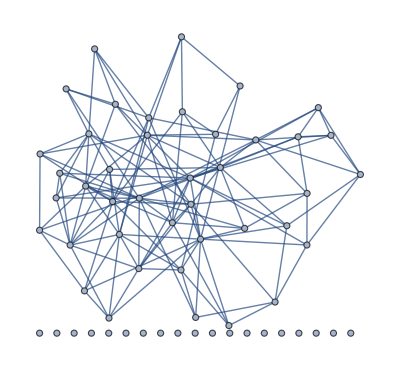

```mathematica
AdjacencyGraph[M1]
```

```mathematica
(* The subgraph M0 defined by the Lemma 2.5, a subgraph of the complexes used for defining codes*)

 M00 = Module[{M00, i, i1, j1, i2, j2}, 
M00 = Table[0, {j, 1, Basedim}, {k, 1, Basedim}];
For[i=1, i<= Length @ StoreInfoLeft, i++, 
i1 = StoreInfoLeft[[i]][[1]]; 
j1 = StoreInfoLeft[[i]][[2]]; 
i2 = StoreInfoRight[[i]][[1]]; 
j2 = StoreInfoRight[[i]][[2]]; 
M00[[i1, j1]]=1; 
M00[[i2, j2]]=1;
];
M00 
];
```

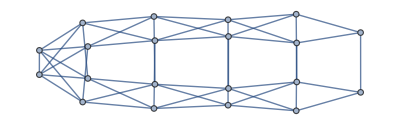

```mathematica
M00graph = AdjacencyGraph[M00]
IncidenceM00 = IncidenceMatrix[M00graph];
M0 = Transpose[IncidenceM00 ]. M00.IncidenceM00;
```

```mathematica
M0Eigs= Sort[Eigenvalues[M0] // N]; 
M0gap = M0Eigs[[-1]] - M0Eigs[[-2]] ;
```

AdjacencyGraph::matsq: 位置 2 处的参数 … 不是一个非空方阵.